```mathematica
(*Define parametric equations*)x[t_]:=(1-t^2)/(1+t^2)
y[t_]:=(2 t)/(1+t^2)

(*Implicify t in terms of x and y*)
tsolx=Solve[x==(1-t^2)/(1+t^2),t];
tsoly=Solve[y==(2 t)/(1+t^2),t];

(*Display the results*)
tsolx
tsoly
```

{{t→-(√(1-x))/(√(1+x))},{t→(√(1-x))/(√(1+x))}}

{{t→(1-√(1-y^2))/y},{t→(1+√(1-y^2))/y}}

```mathematica
(*Define the parametric equations*)x[t_]:=(1-t^2)/(1+t^2)
y[t_]:=(2 t)/(1+t^2)

(*Implicify t in terms of x and y*)
tsolx=t/.Solve[x==(1-t^2)/(1+t^2),t];
tsoly=t/.Solve[y==(2 t)/(1+t^2),t];

(*Substitute expressions for t into x and y equations*)
circlex=Simplify[1+(#+1)/(1-#)&/@tsolx];
circley=Simplify[1+(2-#)/(2 #)&/@tsoly];

(*Display the resulting algebraic equation*)
circlex
circley
```

{(2 √(1+x))/(√(1-x)+√(1+x)),(2 √(1+x))/(-√(1-x)+√(1+x))}

{(1+2 y-√(1-y^2))/(2-2 √(1-y^2)),(1+2 y+√(1-y^2))/(2+2 √(1-y^2))}

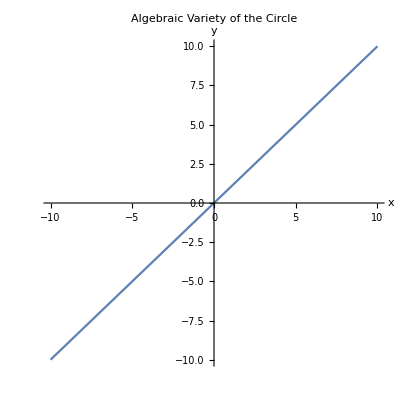

```mathematica
(*Define the algebraic equations*)circlex=1+(#+1)/(1-#)&/@t;
circley=1+(2-#)/(2 #)&/@t;

(*Plot the variety*)
ParametricPlot[{circlex,circley},{t,-10,10},AspectRatio->1,PlotRange->All,AxesLabel->{"x","y"},PlotLabel->"Algebraic Variety of the Circle"]
```

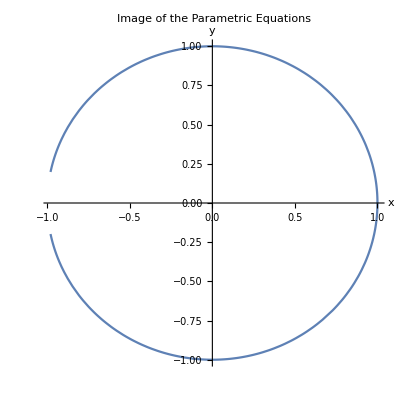

```mathematica
(*Define the parametric equations*)x[t_]:=(1-t^2)/(1+t^2)
y[t_]:=(2 t)/(1+t^2)

(*Plot the image of the parametric equations*)
ParametricPlot[{x[t],y[t]},{t,-10,10},AspectRatio->1,PlotRange->All,AxesLabel->{"x","y"},PlotLabel->"Image of the Parametric Equations"]
```

```mathematica
(*do bazowych rownania wstaiwam do x t = 1 -> (0,1), do y t = -1 (0,-1) -> srodke w (0,0) -> x^2 + y^2 = 1



w x jak t dazy do +/- nieskonczosci to x = 1
w analogicznie y = 0*)
```